Warning: This file REQUIRES “Plot3.nb” to be run through Sec 01. Otherwise, datafiles are not read and parsed.

## Run this for ALL physical couplings

```mathematica
ntwirls=10;
nreps=144;

datsConcat=Table[
Join[dats12ByTwirls[[idx]],dats23ByTwirls[[idx]]]
,{idx,1,ntwirls}];
datsDistinct = {dats12ByTwirls,dats23ByTwirls};
```

## Run this for one physical coupling

```mathematica
ntwirls=5;
nreps=8; (*for pre-calibration runs, this is 2x4=8; postcalibration runs, 2x10=20*)
couplingIdx=6;

datsConcat=Table[
Join[dats12[[couplingIdx,idx]],dats23[[couplingIdx,idx]]]
,{idx,1,ntwirls}];
datsDistinct = {dats12[[couplingIdx]],dats23[[couplingIdx]]};
```

## Rest of code: Run this in either case.

```mathematica
means=Table[
Mean[datsDistinct[[idxbraidword,idxtwirls]]]
,{idxbraidword,1,2},{idxtwirls,1,ntwirls}];
```

```mathematica
getroc=Module[{normTrue,normFalse,idxHypothesis,idxBraidWord,flagSelf,distances,roc},
idxHypothesis=#1;
idxBraidWord=#2;

normTrue=0;
normFalse=0;
distances=Table[
flagSelf=(idxTwirls==idxHypothesis);
If[flagSelf,normTrue +=1,normFalse+=1];
{Norm[datsConcat[[idxTwirls,idxRep]]-means[[idxBraidWord,idxHypothesis]],2], flagSelf}
,{idxTwirls,1,ntwirls},{idxRep,1,nreps}];
distances = Flatten[distances,1];
distances=Sort[distances,#2[[1]]>#1[[1]]&];

roc = Table[
clickTable=distances[[1;;idx]]ᵀ[[2]];
truePositives = Count[clickTable,True]/normTrue;
falsePositives = Count[clickTable,False]/normFalse;
{falsePositives,truePositives}//N
,{idx,1,Dimensions[distances][[1]]}];

roc
]&;
```

```mathematica
roc=Table[
getroc[idxtwirls,idxbraidword]
,{idxbraidword,1,2},{idxtwirls,1,ntwirls}];
```

```mathematica
SetOptions[ListLinePlot,PlotStyle->{Thick,Orange},Frame->True,FrameTicksStyle->FontSize->25,
PlotRange->{{0,1},{0,1}},AspectRatio->1,ImageSize->{640,640},
FrameLabel->{{Style["True Positive",25],None},{Style["False Positive",25],Style["ROC",25]}}];
Manipulate[
Show[ 
ListLinePlot[roc[[idxbraidword,idxtwirls]]]
,
Plot[x,{x,0,1},PlotStyle->{Gray,Dashed}]
]
,{idxbraidword,1,2,1},{idxtwirls,1,ntwirls,1}]
```

## Consolidated version of the above, for exporting

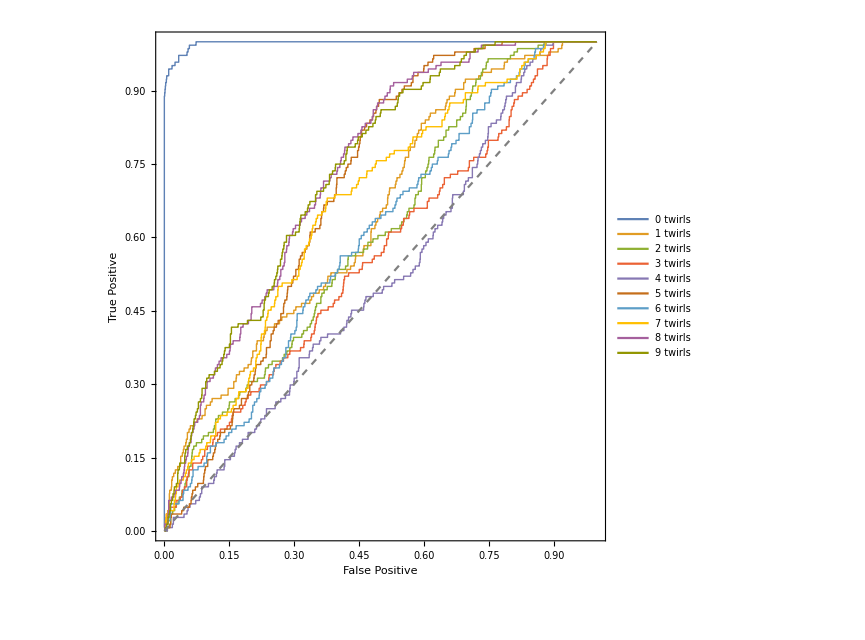

```mathematica
SetOptions[ListLinePlot,PlotStyle->{Thick},Frame->True,FrameTicksStyle->FontSize->25,
PlotRange->{{0,1},{0,1}},AspectRatio->1,ImageSize->{640,640},
FrameLabel->{{Style["True Positive",25],None},{Style["False Positive",25],Style["ROC, σ_23^k as null hypothesis",25]}}];
labels=Table[Style[StringJoin[ToString[k]," twirls"],15],{k,0,9}];
Show[ 
ListLinePlot[roc[[2]]
,PlotLegends->Placed[labels,{0.7,0.3}]
]
,
Plot[x,{x,0,1},PlotStyle->{Gray,Dashed}]
]
```